## KDE: Ejemplo "V sini"

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/michel/cursos/pregrado

```mathematica
vsini=Import["DataVSini.dat"]//Flatten;
```

```mathematica
Length@vsini
```

11818

```mathematica
Select[vsini,!NumberQ]
```

{}

```mathematica
Min@vsini
```

0

```mathematica
Max@vsini
```

29

```mathematica
Count[vsini,0]
```

133

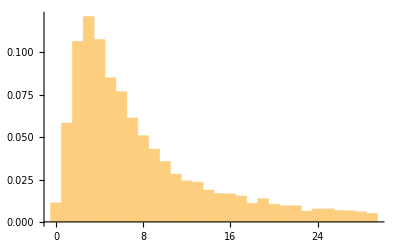

```mathematica
Histogram[vsini,Automatic,"PDF"]
```

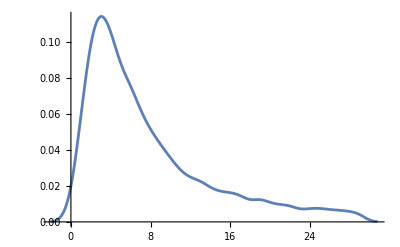

```mathematica
SmoothHistogram@vsini
```

```mathematica
dist0=SmoothKernelDistribution[vsini]
```

DataDistribution[…]

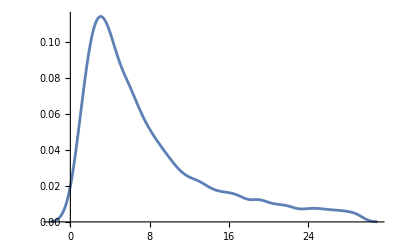

```mathematica
grd0=Plot[PDF[dist0,x],{x,-2,31}]
```

```mathematica
Probability[x<0,x\[Distributed]dist0]
```

0.0107542

```mathematica
Probability[x>=0,x\[Distributed]dist0]
```

0.989246

```mathematica
dist1=SmoothKernelDistribution[vsini,Automatic,{"Bounded",{0,35},"Gaussian"}];
```

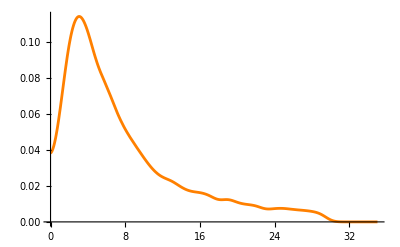

```mathematica
grd1=Plot[PDF[dist1,x],{x,0,35},PlotStyle->Orange]
```

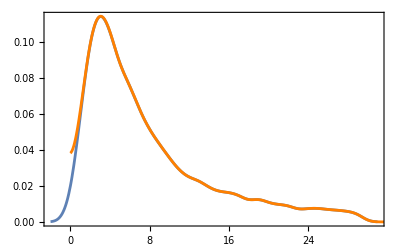

```mathematica
Show[grd0,grd1,Frame->True]
```

```mathematica
vsini2=-vsini;
```

```mathematica
dist2=SmoothKernelDistribution[vsini,Automatic,"Gaussian"]
```

DataDistribution[…]

```mathematica
dist3=SmoothKernelDistribution[vsini2,Automatic,"Gaussian"]
```

DataDistribution[…]

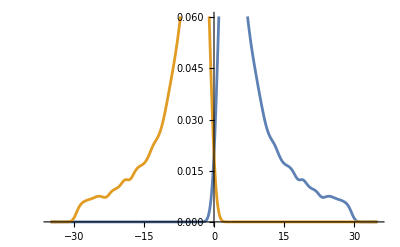

```mathematica
Plot[{PDF[dist2,x],PDF[dist3,x]},{x,-35,35}]
```

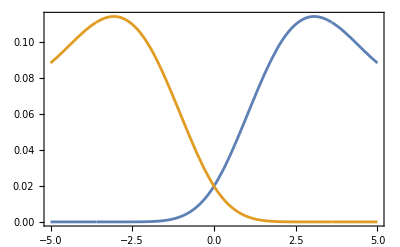

```mathematica
Plot[{PDF[dist2,x],PDF[dist3,x]},{x,-5,5},Frame->True]
```

```mathematica
dist4=ProbabilityDistribution[PDF[dist2,x]-PDF[dist3,x],{x,0,35}]
```

ProbabilityDistribution[-(Piecewise[{{InterpolatingFunction[…][x], -32.6033≤x≤3.60327}, {0, True}}])+(Piecewise[{{InterpolatingFunction[…][x], -3.60327≤x≤32.6033}, {0, True}}]),{x,0,35}]

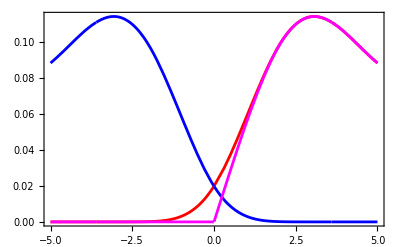

```mathematica
Plot[{PDF[dist2,x],PDF[dist3,x],PDF[dist4,x]},{x,-5,5},PlotStyle->{Red,Blue,Magenta},Frame->True]
```

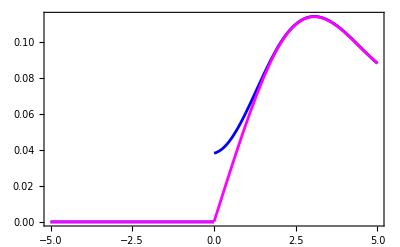

```mathematica
Plot[{PDF[dist1,x],PDF[dist4,x]},{x,-5,5},PlotStyle->{Blue,Magenta},Frame->True]
```

```mathematica
cte=NIntegrate[PDF[dist4,x],{x,0,50}]
```

0.978492

```mathematica
dist5=ProbabilityDistribution[(1/cte)(PDF[dist2,x]-PDF[dist3,x]),{x,0,35}];
```

```mathematica
NIntegrate[PDF[dist5,x],{x,0,50}]
```

1.

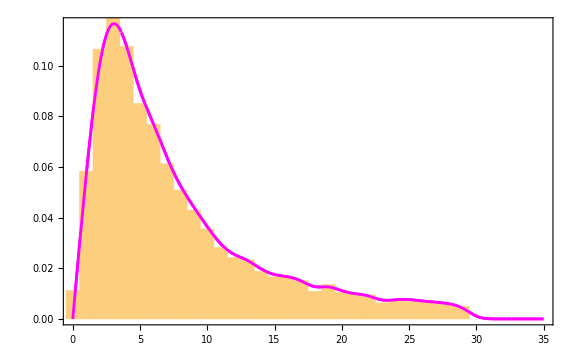

```mathematica
Show[Plot[PDF[dist5,x],{x,0,35},PlotStyle->Magenta],Histogram[vsini,Automatic,"PDF"],Plot[PDF[dist5,x],{x,0,35},PlotStyle->Magenta],Frame->True,ImageSize->Large]
```

## Ejercicio : de la seccion "A rule-of-thumb bandwidth estimator" de la pagina web "https://en.wikipedia.org/wiki/Kernel_density_estimation”

```mathematica
dist=MixtureDistribution[{1.,1.},{NormalDistribution[-10,1],NormalDistribution[10,1]}]
```

MixtureDistribution[{1.,1.},{NormalDistribution[-10,1],NormalDistribution[10,1]}]

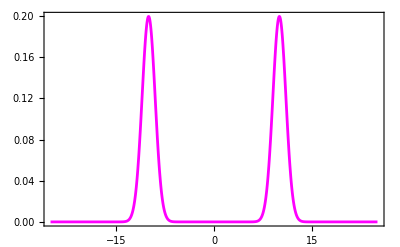

```mathematica
gr0=Plot[PDF[dist,x],{x,-25.,25.},Frame->True,PlotRange->All,PlotStyle->Magenta]
```

```mathematica
datos=RandomVariate[dist,1000];
```

```mathematica
kde=SmoothKernelDistribution[datos]
```

DataDistribution[…]

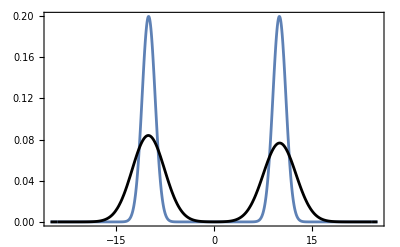

```mathematica
Show[gr0,Plot[PDF[kde,x],{x,-25.,25.},Frame->True,PlotRange->All,PlotStyle->Black]]
```

### Ancho de Banda

```mathematica
nobw={"Silverman","LeastSquaresCrossValidation","Oversmooth","Scott","SheatherJones","StandardDeviation","StandardGaussian"};
```

```mathematica
noker={"Epanechnikov","Gaussian"};
```

```mathematica
dists=Table[SmoothKernelDistribution[datos,i,noker[[1]]],{i,nobw}];
```

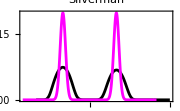
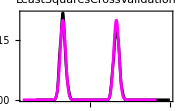
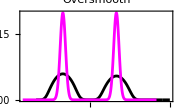
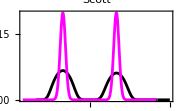
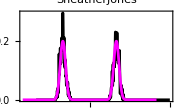
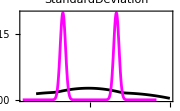
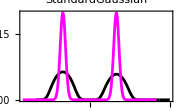

```mathematica
Table[Show[Plot[PDF[dists[[k]],x],{x,-20,30},PlotStyle->Black,PlotLabel->nobw[[k]],PlotRange->All,Frame->True,Axes->False],gr0,ImageSize->Small],{k,Length@dists}]
```

```mathematica
dists2=Table[SmoothKernelDistribution[datos,i,noker[[2]]],{i,nobw}];
```

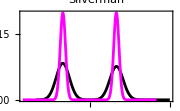
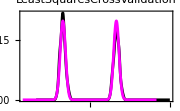
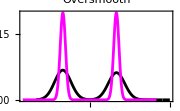
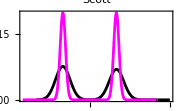
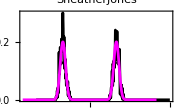
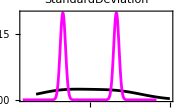
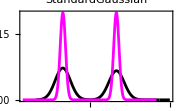

```mathematica
Table[Show[Plot[PDF[dists2[[k]],x],{x,-20,30},PlotStyle->Black,PlotLabel->nobw[[k]],PlotRange->All,Frame->True,Axes->False],gr0,ImageSize->Small],{k,Length@dists}]
```

```mathematica
𝒟=SmoothKernelDistribution[datos,{"Adaptive",Automatic,1.}];
```

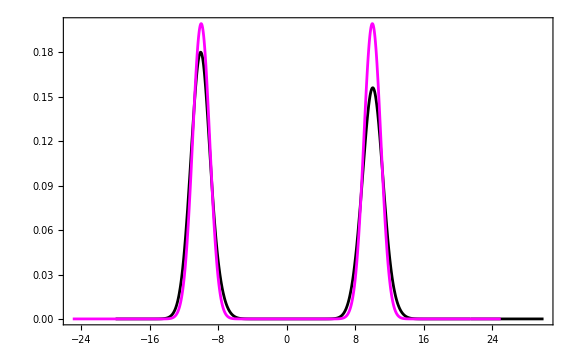

```mathematica
Show[Plot[PDF[𝒟,x],{x,-20,30},PlotStyle->Black,PlotRange->All,Frame->True,Axes->False],gr0,ImageSize->Large]
```